```mathematica
(* 4-state *)
Clear["Global`*"]
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Initial condition*)
p0 = {a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)};
(*Direction solution of the Bellman equation*)
V=p0.Inverse[IdentityMatrix[4] - gamma*Pmat].Rmat;
```

{gamma→0.666667}

{gamma→0.666667}

FindRoot::jsing: Encountered a singular Jacobian at the point {gamma} = {0.8}. Try perturbing the initial point(s).

{gamma→0.8}

{gamma→0.65434}

{gamma→0.638541}

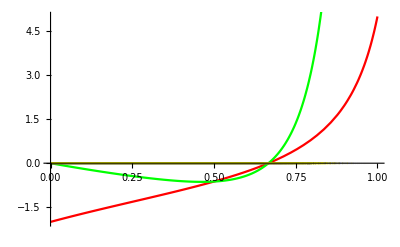

```mathematica
(*Prisoner's dilemma*)
R=3;S=0;T=5;P=1;

a0v=0;a1v=11/13;a2v=1/2;a3v=7/26;a4v=0;
b0v=1; b1v=0;b2v=0;b3v=0;b4v=1;

a0v = 1;a1v=1;a2v=0.2;a3v=1;a4v=0.5;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;

(* V1 *)
a0=a0v;a1=a1v;a2=a2v;a3=a3v;a4=a4v;
b0=b0v;b1=b1v;b2=b2v;b3=b3v;b4=b4v;

Clear[a0];
Va0 = D[V,a0];
a0=a0v;
FindRoot[Va0,{gamma,0.8}]
plt0 = Plot[Va0,{gamma,0,1},PlotStyle->Red];

Clear[a1];
Va1 = D[V,a1];
a1=a1v;
FindRoot[Va1,{gamma,0.8}]
plt1 = Plot[Va1,{gamma,0,1},PlotStyle->Green];

Clear[a2];
Va2 = D[V,a2];
a2=a2v;
FindRoot[Va2,{gamma,0.8}]
plt2 = Plot[Va2,{gamma,0,1},PlotStyle->Blue];

Clear[a3];
Va3 = D[V,a3];
a3=a3v;
FindRoot[Va3,{gamma,0.8}]
plt3 = Plot[Va3,{gamma,0,1},PlotStyle->Black];

Clear[a4];
Va4 = D[V,a4];
a4=a4v;
FindRoot[Va4,{gamma,0.8}]
plt4 = Plot[Va4,{gamma,0,1},PlotStyle->Yellow];

Show[plt0,plt1,plt2,plt3,plt4]
```

```mathematica
(*5-state -----------------------------------------------------*)
Clear["Global`*"]
(*Reward structure for player a (initial, CC, CD, DC, DD)*)
Rmat ={0,R,S,T,P};
(*Transition matrix (P_ij = prob. of going from i to j)*)
Pmat = {{0,a0*b0,a0*(1-b0),(1-a0)*b0,(1-a0)*(1-b0)},{0,a1*b1,a1*(1-b1),(1-a1)*b1,(1-a1)*(1-b1)},{0,a2*b2,a2*(1-b2),(1-a2)*b2,(1-a2)*(1-b2)},{0,a3*b3,a3*(1-b3),(1-a3)*b3,(1-a3)*(1-b3)},{0,a4*b4,a4*(1-b4),(1-a4)*b4,(1-a4)*(1-b4)}};
(*Direction solution of the Bellman equation*)
V=Inverse[IdentityMatrix[5] - gamma*Pmat].Rmat;
```

```mathematica
(*Series expansion of the solution*)
Series[V,{gamma,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+a0 S-a0 b0 S+b0 T-a0 b0 T) gamma+O[gamma]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+a1 S-a1 b1 S+b1 T-a1 b1 T) gamma+O[gamma]^2,S+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+a2 S-a2 b2 S+b2 T-a2 b2 T) gamma+O[gamma]^2,T+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+a3 S-a3 b3 S+b3 T-a3 b3 T) gamma+O[gamma]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+a4 S-a4 b4 S+b4 T-a4 b4 T) gamma+O[gamma]^2}

```mathematica
(*Reward structure for player b (initial, CC, CD, DC, DD)*)
(*Note: CD still means player a = C, player b = D*)
Rmat2 ={0,R,T,S,P};
(*Direction solution of the Bellman equation*)
V2=Inverse[IdentityMatrix[5] - gamma2*Pmat].Rmat2;
```

```mathematica
Series[V2,{gamma2,0,1}]
```

{(P-a0 P-b0 P+a0 b0 P+a0 b0 R+b0 S-a0 b0 S+a0 T-a0 b0 T) gamma2+O[gamma2]^2,R+(P-a1 P-b1 P+a1 b1 P+a1 b1 R+b1 S-a1 b1 S+a1 T-a1 b1 T) gamma2+O[gamma2]^2,T+(P-a2 P-b2 P+a2 b2 P+a2 b2 R+b2 S-a2 b2 S+a2 T-a2 b2 T) gamma2+O[gamma2]^2,S+(P-a3 P-b3 P+a3 b3 P+a3 b3 R+b3 S-a3 b3 S+a3 T-a3 b3 T) gamma2+O[gamma2]^2,P+(P-a4 P-b4 P+a4 b4 P+a4 b4 R+b4 S-a4 b4 S+a4 T-a4 b4 T) gamma2+O[gamma2]^2}

```mathematica
(*Gradients -----------------------------------------------------------------------------------------------------------------------------------*)
(*DVa0total = InputForm[D[Total[V],a0]];*)
dVa0 = D[Total[V],a0];dVa1 = D[Total[V],a1];dVa2= D[Total[V],a2];dVa3 = D[Total[V],a3];dVa4 = D[Total[V],a4];
dVb0 = D[Total[V],b0];dVb1 = D[Total[V],b1];dVb2= D[Total[V],b2];dVb3 = D[Total[V],b3];dVb4 = D[Total[V],b4];

dV2b0 = D[Total[V2],b0];dV2b1 = D[Total[V2],b1];dV2b2= D[Total[V2],b2];dV2b3 = D[Total[V2],b3];dV2b4 = D[Total[V2],b4];

(*Hessian*)
dVdab = D[Total[V],{{a0,a1,a2,a3,a4,b0,b1,b2,b3,b4},2}];
(*2nd term in (4.4) w/o learning rates*)
LOLA = dVdab[[1;;5,6;;10]].{dV2b0,dV2b1,dV2b2,dV2b3,dV2b4};
Dimensions[LOLA]
```

{5}

```mathematica
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa0_total.txt",{dVa0}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa1_total.txt",{dVa1}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa2_total.txt",{dVa2}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa3_total.txt",{dVa3}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVa4_total.txt",{dVa4}];

Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb0_total.txt",{dVb0}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb1_total.txt",{dVb1}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb2_total.txt",{dVb2}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb3_total.txt",{dVb3}];
Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\DVb4_total.txt",{dVb4}];

Export["D:\\USB_send\\Project_Negotiation\\prospectiveporpoise\\LOLA_total.txt",{LOLA}];
```

```mathematica
Series[LOLA,{gamma2,0,2}]
```

```mathematica
LOLA
```

{1,3,(-(((-gamma+a0 gamma+gamma^2-a0 gamma^2-a0 a1 gamma^2+a2 gamma^2-a3 gamma^2+43+a0 a1 b2 gamma^4-a1 a2 b2 gamma^4-a0 a3 b2 gamma^4+a2 a3 b2 gamma^4-a0 a1 b3 gamma^4+a0 a2 b3 gamma^4+a1 a3 b3 gamma^4-a2 a3 b3 gamma^4) (1) P)/(1-gamma-a2 gamma+156+a2 a3 b3 b4 gamma^4+a1 a4 b3 b4 gamma^4-a2 a4 b3 b4 gamma^4)^2)-((1) (1) R)/(1)^2+6+((gamma^2-a0 gamma^2-gamma^3+18+a2 b4 gamma^4) T)/(1-gamma-a2 gamma+157+a1 a4 b3 b4 gamma^4-a2 a4 b3 b4 gamma^4)) (1)+3+1}
 |  |  |  |

```mathematica
(*ZD-strategy -----------------------------------------------------------------------------------------------------------------------------------*)
```

```mathematica
p[chi_,phi_] := {1-2*phi*(chi-1),1-phi*(4*chi+1),phi*(chi+4),0}
```

```mathematica
p[3,1/26] (*Standard at midpoint chi)*)
p[3,2/26]
p[3,1/52]
```

{11/13,1/2,7/26,0}

{9/13,0,7/13,0}

{12/13,3/4,7/52,0}

```mathematica
(*Generic crit. gamma -------------------------------------------------------------------------------------------------------------------------------*)
```

{gamma→0.666667}

{gamma→0.666667}

{gamma→0.666667}

«2 more identical outputs»

{gamma2→0.833333}

{gamma2→0.833333}

{gamma2→0.636573}

{gamma2→0.833333}

{gamma2→0.769231}

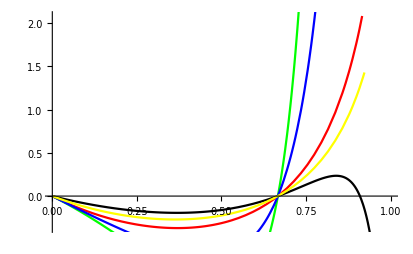

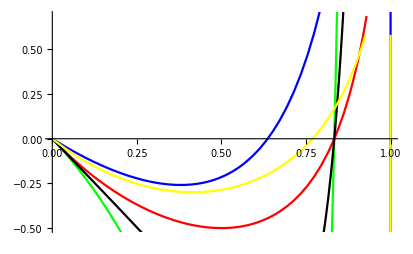

```mathematica
Clear[a0,a1,a2,a3,a4,b0,b1,b2,b3,b4,gamma,gamma2];

(*Game type ------------------------------------------------------*)
(*Prisoner's dilemma*)
R=3;S=0;T=5;P=1;
(*Battle of the sexes*)
R=0;S=1;T=2;P=0;

(*Actual*)
R=3;S=0;T=5;P=1;

(*Init param ------------------------------------------------------*)
(*All-coop*)
a0v = 1;a1v=1;a2v=1;a3v=1;a4v=1;
b0v=1; b1v=1;b2v=1;b3v=1;b4v=1;
(*All-defect*)
a0v = 0;a1v=0;a2v=0;a3v=0;a4v=0;
b0v=0; b1v=0;b2v=0;b3v=0;b4v=0;
(*All-Random*)
a0v = 0.5;a1v=0.5;a2v=0.5;a3v=0.5;a4v=0.5;
b0v=0.5; b1v=0.5;b2v=0.5;b3v=0.5;b4v=0.5;
(*tit-for-tat*)
a0v = 1;a1v=1;a2v=0;a3v=1;a4v=0;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0;
(*Everything positive regime*)
a0v = 1;a1v=1;a2v=0.2;a3v=1;a4v=0.5;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;
(*ZD*)
a0v=0;a1v=11/13;a2v=1/2;a3v=7/26;a4v=0;
a0v=0;a1v=9/13;a2v=0;a3v=7/13;a4v=0;
a0v=0;a1v=12/13;a2v=3/4;a3v=7/52;a4v=0;

(*Actual*)
a0v = 0.32890504;a1v=0.72718054;a2v=0.29262048;a3v=0.60808543999;a4v=0.120000974;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;

a0v = 1;a1v=1;a2v=0.2;a3v=1;a4v=0.5;
b0v=1; b1v=1;b2v=1;b3v=0;b4v=0.5;


(*------------------------------------------------------*)

(* V1 *)
a0=a0v;a1=a1v;a2=a2v;a3=a3v;a4=a4v;
b0=b0v;b1=b1v;b2=b2v;b3=b3v;b4=b4v;

Clear[a0];
Va0 = D[Total[V],a0];
a0=a0v;
FindRoot[Va0,{gamma,0.8}]
plt0 = Plot[Va0,{gamma,0,1},PlotStyle->Red];

Clear[a1];
Va1 = D[Total[V],a1];
a1=a1v;
FindRoot[Va1,{gamma,0.8}]
plt1 = Plot[Va1,{gamma,0,1},PlotStyle->Green];

Clear[a2];
Va2 = D[Total[V],a2];
a2=a2v;
FindRoot[Va2,{gamma,0.8}]
plt2 = Plot[Va2,{gamma,0,1},PlotStyle->Blue];

Clear[a3];
Va3 = D[Total[V],a3];
a3=a3v;
FindRoot[Va3,{gamma,0.8}]
plt3 = Plot[Va3,{gamma,0,1},PlotStyle->Black];

Clear[a4];
Va4 = D[Total[V],a4];
a4=a4v;
FindRoot[Va4,{gamma,0.8}]
plt4 = Plot[Va4,{gamma,0,1},PlotStyle->Yellow];

pltVsum = Plot[Va0+Va1+Va2+Va3+Va4,{gamma,0,1},PlotStyle->Brown];

(* V2 *)
a0=a0v;a1=a1v;a2=a2v;a3=a3v;a4=a4v;
b0=b0v;b1=b1v;b2=b2v;b3=b3v;b4=b4v;

Clear[b0];
Vb0 = D[Total[V2],b0];
b0=b0v;
FindRoot[Vb0,{gamma2,0.8}]
pltb0 = Plot[Vb0,{gamma2,0,1},PlotStyle->Red];

Clear[b1];
Vb1 = D[Total[V2],b1];
b1=b1v;
FindRoot[Vb1,{gamma2,0.8}]
pltb1 = Plot[Vb1,{gamma2,0,1},PlotStyle->Green];

Clear[b2];
Vb2 = D[Total[V2],b2];
b2=b2v;
FindRoot[Vb2,{gamma2,0.8}]
pltb2 = Plot[Vb2,{gamma2,0,1},PlotStyle->Blue];

Clear[b3];
Vb3 = D[Total[V2],b3];
b3=b3v;
FindRoot[Vb3,{gamma2,0.95}]
pltb3 = Plot[Vb3,{gamma2,0,1},PlotStyle->Black];

Clear[b4];
Vb4 = D[Total[V2],b4];
b4=b4v;
FindRoot[Vb4,{gamma2,0.8}]
pltb4 = Plot[Vb4,{gamma2,0,1},PlotStyle->Yellow];

pltV2sum = Plot[Vb0+Vb1+Vb2+Vb3+Vb4,{gamma2,0,1},PlotStyle->Brown];

Show[plt0,plt1,plt2,plt3,plt4]
Show[pltb0,pltb1,pltb2,pltb3,pltb4]
```